## Parameter Initialisation and Stationarity Checks

```mathematica
(* =====Parameters=====*)
ω=0.25;        (*baseline variance*)
α=0.1;         (*ARCH term coefficient*)
β=0.7;        (*GARCH term coefficient*)
λ=0.2;        (*GJR asymmetry coefficient*)
aPar=4;           (*Beta shape parameter'a', not necessarily integer*)
σ1sq=1.05;        (*initial conditional variance sigma_1^2*)

(* =====Stationarity check=====*)
stationarityLHS=α+(λ/2)+β;
If[stationarityLHS>=1,Print["Warning: Stationarity condition violated! α + λ/2 + β = ",N[stationarityLHS], " ≥ 1"],Print["Stationarity condition satisfied: α + λ/2 + β = ",N[stationarityLHS], " < 1"]];

(* =====Derived constants=====*)
bPar=2*aPar +1;
Ca=1/(2^(2*aPar-1)*Sqrt[bPar] Beta[aPar,aPar]);

(* =====Print parameters as numeric=====*)
Print["Parameter values:"];
Print["  ω     = ",N[ω]];
Print["  α     = ",N[α]];
Print["  β     = ",N[β]];
Print["  λ     = ",N[λ]];
Print["  a     = ",N[aPar]];
Print["  σ1^2  = ",N[σ1sq]];

Print["Derived constants:"];
Print["  b     = ",N[bPar]];
Print["  C_a   = ",N[Ca]];
```

Stationarity condition satisfied: α + λ/2 + β = 0.9 < 1

Parameter values:

ω     = 0.25

α     = 0.1

β     = 0.7

λ     = 0.2

a     = 4.

σ1^2  = 1.05

Derived constants:

b     = 9.

C_a   = 0.364583

## Transformed Beta Densities

## Innovations Density

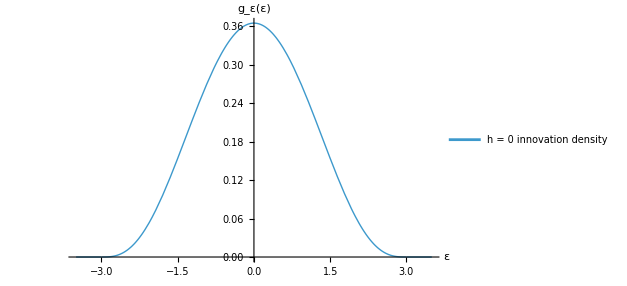

normalisation value:

1.

Maximum absolute value in support:

3.

```mathematica
(*0-step (innovation) density for ε_t*)
gEps[e_]:=Piecewise[{{Ca*(1-e^2/(2 aPar+1))^(aPar-1),-Sqrt[2 aPar+1]<=e<=Sqrt[2 aPar+1]}},0];

(*Max absolute value in support*)
eMax=Sqrt[2 aPar+1];

(*Plot innovation density*)
Plot[gEps[e],{e,-eMax-0.5,eMax+0.5},PlotRange->All,AxesLabel->{"ε","g_ε(ε)"},PlotLegends->Placed[{"h = 0 innovation density"},{Right,Top}],PlotStyle->Thick]

(*Check integration to 1*)
Print["normalisation value:"];
NIntegrate[gEps[e],{e,-eMax,eMax}]

(*Show support bound*)
Print["Maximum absolute value in support:"];
Print[N[eMax]]
```

#### Moments checks:

```mathematica
(* =====h=0 (innovations)=====*)
(*Assumes:parameters, eMax, gEps is defined.*)

m1h0=NIntegrate[x*gEps[x],{x,-eMax,eMax},Method->{"LocalAdaptive"},MaxRecursion->20,AccuracyGoal->12,PrecisionGoal->12];

m2h0=NIntegrate[x^2*gEps[x],{x,-eMax,eMax},Method->{"LocalAdaptive"},MaxRecursion->20,AccuracyGoal->12,PrecisionGoal->12];

Print["=== h = 0 ==="];
Print["E[x_0]           = ",N[m1h0],"   (expected 0)"];
Print["E[x_0^2]         = ",N[m2h0],"   (expected 1)"];
Print["Abs diff of second moment  = ",Abs[m2h0-1.0]];
```

=== h = 0 ===

E[x_0]           = 0.   (expected 0)

E[x_0^2]         = 1.   (expected 1)

Abs diff of second moment  = 0.

## One-Step-Ahead Density, g (with variable transform)

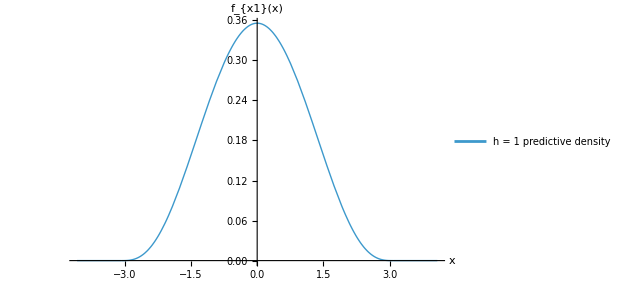

Normalisation:

1.

Maximum value in support (should be sqrt(2a+1)*σ1):

3.07409

```mathematica
σ1=Sqrt[σ1sq];

(*g on the dimensionless argument u=(x/σ1)^2=ε^2*)
gCore[u_]:=Piecewise[{{Ca*(1-u/(2 aPar+1))^(aPar-1),0<=u<=(2 aPar+1)}},0];

(*One-step-ahead predictive density for the return x_1*)
fx1[x_]:=(1/σ1)*gCore[(x/σ1)^2];

(*Plot over the correct support*)
xMax1=Sqrt[(2 aPar+1)]*σ1;
Plot[fx1[x],{x,-xMax1 - 1,xMax1 + 1},PlotRange->All,AxesLabel->{"x","f_{x1}(x)"},PlotLegends->Placed[{"h = 1 predictive density"},{Right,Top}],PlotStyle->Thick]

(*Sanity check:integrates to~1 over the support*)
Print["Normalisation:"]
NIntegrate[fx1[x],{x,-xMax1,xMax1}]

(*Check the support bounds:*)
Print["Maximum value in support (should be sqrt(2a+1)*σ1):"]
Print[xMax1]
```

#### Moments checks:

```mathematica
(* =====h=1=====*)
(*Assumes: parameters, fx1, xMax1 are defined.*)

m1h1=NIntegrate[x*fx1[x],{x,-xMax1,xMax1},Method->{"LocalAdaptive"},MaxRecursion->20,AccuracyGoal->12,PrecisionGoal->12];

m2h1=NIntegrate[x^2*fx1[x],{x,-xMax1,xMax1},Method->{"LocalAdaptive"},MaxRecursion->20,AccuracyGoal->12,PrecisionGoal->12];

Print["=== h = 1 ==="];
Print["E[x_1]           = ",N[m1h1],"   (expected 0)"];
Print["E[x_1^2]         = ",N[m2h1],"   (expected ",N[σ1sq],")"];
Print["Abs diff of second moment  = ",Abs[m2h1-N[σ1sq]]];
```

=== h = 1 ===

E[x_1]           = 0.   (expected 0)

E[x_1^2]         = 1.05   (expected 1.05)

Abs diff of second moment  = 2.22045×10^-16

## Two-Step-Ahead Density, f_{x_2}

### Using 2F1 representation for our Appell

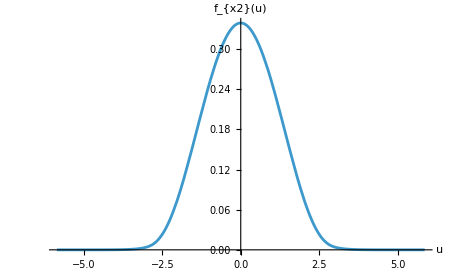

First support boundary:              ±2.97741

Second support boundary:             ±4.16773

Third support boundary (0 outside):  ±5.86345

Normalisation: 1.

```mathematica
(* =====h=2 building blocks (Lemma 3.1),using only 2F1=====*)
(*assumes parameters were initialized already, as in earlier block*)
barKappa1=ω+β*σ1sq;

alpha1[s_]:=α+λ*(1-s)/2;
zeta1[s_]:=alpha1[s]*bPar*σ1sq/barKappa1;

tLower[s_,u_?NumericQ]:=Module[{num},num=(u^2/bPar-barKappa1)/(alpha1[s]*bPar*σ1sq);
Max[0,Min[1,num]]];

U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+alpha1[s]*bPar*σ1sq);

(*Gauss block:{}_2F_1(j+1/2,1/2;a+1/2;-\zeta*s*t)*)
gaussTerm[j_,s_,t_]:=Hypergeometric2F1[j+1/2,1/2,aPar+1/2,-zeta1[s]*t];

(*---- lower-limit integral on[0,tL] WITHOUT Appell F1----\int_0^{tL} t^{-1/2} (1-t)^{a-1} (1+\zeta t)^-(j+1/2) dt=Sum_{n>=0} (-1)^n Binomial[a-1,n]*tL^(n+1/2)/(n+1/2)*2F1(n+1/2,j+1/2;n+3/2;-\zeta tL) In the lemma,the normalized subtraction divides by Beta[1/2,aPar].*)
lower2F1[j_,s_,u_?NumericQ,nMax_:30]:=Module[{tL=tLower[s,u],z=zeta1[s],θ=j+1/2},If[tL==0.,0.,Sum[(-1)^n*Binomial[aPar-1,n]*tL^(n+1/2)/(n+1/2)*Hypergeometric2F1[n+1/2,θ,n+3/2,-z*tL],{n,0,nMax}]/Beta[1/2,aPar]]];

(*truncation levels*)
maxJ=30;   (*outer j-sum*)
nMax=10;   (*inner n-sum for the lower-limit integral*)

(* =====Two-step unconditional return density f_{x2}(u)=====*)
Clear[fx2]
fx2[u_?NumericQ]:=Module[{u2=u^2,inner,val},Which[(*Case 1:0<=u^2<=U1*)0<=u2<=U1,inner[j_]:=(1/2) Sum[gaussTerm[j,s,1],{s,{-1,1}}];
val=Ca*N@Sum[(-1)^j*Binomial[aPar-1,j]*(u2/bPar)^j*barKappa1^(-(j+1/2))*inner[j],{j,0,maxJ}],(*Case 2:U1<u^2<=U1max(+1)*)U1<u2<=U1max[+1],inner[j_]:=(1/2) Sum[With[{tL=tLower[s,u]},gaussTerm[j,s,1]-lower2F1[j,s,u,nMax]],{s,{-1,1}}];
val=Ca*N@Sum[(-1)^j*Binomial[aPar-1,j]*(u2/bPar)^j*barKappa1^(-(j+1/2))*inner[j],{j,0,maxJ}],(*Case 3:U1max(+1)<u^2<U1max(-1)*)U1max[+1]<u2<U1max[-1],inner[j_]:=With[{tLm=tLower[-1,u]},(1/2)*(gaussTerm[j,-1,1]-lower2F1[j,-1,u,nMax])];
val=Ca*N@Sum[(-1)^j*Binomial[aPar-1,j]*(u2/bPar)^j*barKappa1^(-(j+1/2))*inner[j],{j,0,maxJ}],(*Outside support*)True,val=0.];
val];

(* =====Support and quick checks=====*)
uMax2=Sqrt[U1max[-1]];

(*Plot*)
Plot[fx2[u],{u,-uMax2,uMax2},PlotRange->All,AxesLabel->{"u","f_{x2}(u)"}]

(*Print support boundaries*)
Print["First support boundary:              ±",Sqrt[U1]];
Print["Second support boundary:             ±",Sqrt[U1max[+1]]];
Print["Third support boundary (0 outside):  ±",uMax2];
Print["Normalisation: ",NIntegrate[fx2[u],{u,-uMax2,uMax2}]];
```

#### Moments checks:

```mathematica
(* =====h=2=====*)
(*Assumes: parameters, fx2, uMax2 are defined.*)

m1h2=NIntegrate[u*fx2[u],{u,-uMax2,uMax2},Method->{"LocalAdaptive"},MaxRecursion->20,AccuracyGoal->12,PrecisionGoal->12];

m2h2=NIntegrate[u^2*fx2[u],{u,-uMax2,uMax2},Method->{"LocalAdaptive"},MaxRecursion->20,AccuracyGoal->12,PrecisionGoal->12];

Print["=== h = 2 ==="];
Print["E[x_2]           = ",N[m1h2],"   (expected 0)"];
Print["E[x_2^2]         = ",N[m2h2]];
```

=== h = 2 ===

E[x_2]           = -7.75373×10^-15   (expected 0)

E[x_2^2]         = 1.195

## Innovations, f_{x_1}, f_{x_2} on the Same Graph

```mathematica
(*Combined plot:h=0,h=1,h=2 (GJR)*)
Plot[Evaluate@{gEps[x],fx1[x],fx2[x]},{x,-5,5},PlotRange->All,PlotStyle->{},PlotLegends->Placed[{"Beta-Derived Innovations","h = 1","h = 2 (GJR)"},{Right,Top}],AxesLabel->{}]
```

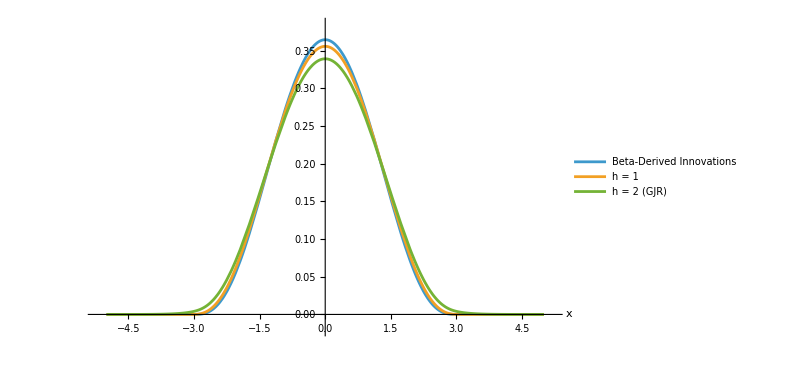

```mathematica
(* ===Right-tail zoom for h=0,1,2 only===*)

Plot[Evaluate@{gEps[x],fx1[x],fx2[x]},{x,2,4},PlotRange->All,PlotStyle->{},PlotLegends->Placed[{"Beta-derived innovations","h = 1","h = 2 (GJR)"},{Right,Top}],AxesLabel->{},GridLines->Automatic]
```

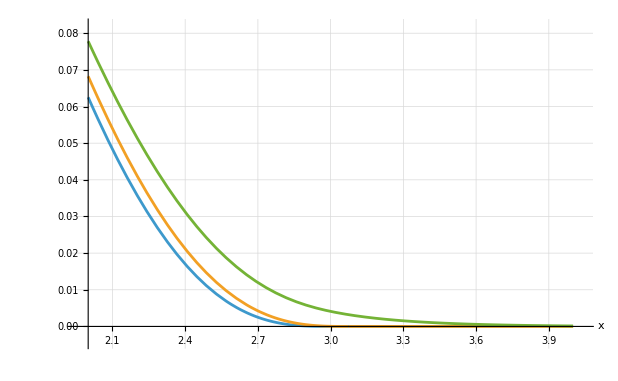

## Three-step-ahead Density, f_{x_3}

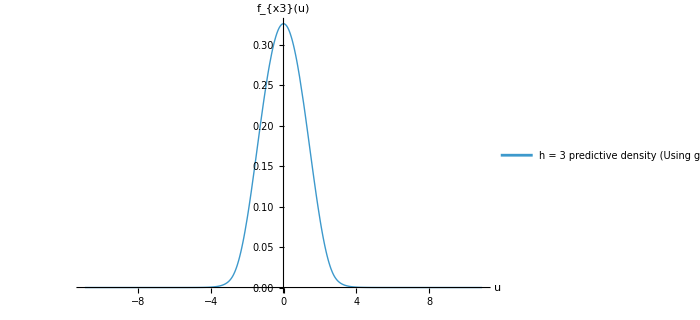

Pathwise sqrt(U3^max):

path {-1,-1} :    ±10.9152

path {-1,1} :    ±7.5669

path {1,-1} :    ±7.82994

path {1,1} :    ±5.48106

Normalisation (fx3): 1.

```mathematica
(* =====h=3 predictive density via kernel integral=====*)
(*Assumes parameters are already defined*)
(*Alpha on a sign:s\in {-1,+1}*)
alphaS[s_]:=α+λ*(1-s)/2;

(*Per-step v-upper-bounds after the y-change:0<v_t<(alphaS/β) b*)
vMax[s_]:=(alphaS[s]/β)*bPar;

(*Recursion in t-coordinates:v1=vMax[s1] t1^2,v2=vMax[s2] t2^2*)
sigma2sqT[t1_,s1_]:=ω+β*(1+vMax[s1]*t1^2)*σ1sq;
sigma3sqT[t1_,t2_,s1_,s2_]:=ω+β*(1+vMax[s2]*t2^2)*sigma2sqT[t1,s1];

(*Beta-kernel on squares:g(s)=C_a (1-s/b)_+^{a-1}*)
gCore[s_]:=Piecewise[{{Ca*(1-s/bPar)^(aPar-1),0<=s<=bPar}},0];

(*Path prefactor γ_{3,s}=β^2/(α1 α2)*)
gamma3[s1_,s2_]:=β^2/(alphaS[s1]*alphaS[s2]);

(*Path-conditional squared-return density f_{x3^2|s}(w) as a 2D integral in t1,t2∈(0,1)*)
fPathX3sq[w_?NumericQ,s1_,s2_]:=Module[{v1m=vMax[s1],v2m=vMax[s2],γ=gamma3[s1,s2],pref,integrand},If[w<=0.,Return[0.]];(*^ guard for w=0 in the kernel form*)
(*Change-of-variables v=vMax t^2 removes endpoint sqrt singularities; Jacobian gives 4 Sqrt[v1m v2m]*)
pref=Sqrt[γ/w]*4*Sqrt[v1m*v2m];
integrand[t1_,t2_]:=Module[{σ3sq=sigma3sqT[t1,t2,s1,s2]},(1/Sqrt[σ3sq])*gCore[bPar*t1^2]*gCore[bPar*t2^2]*gCore[w/σ3sq]];
NIntegrate[pref*integrand[t1,t2],{t1,0,1},{t2,0,1}]];

(*Unconditional h=3 return density:f_{x3}(u)= |u| *2^{-(3-1)}*Σ_s f_{x3^2|s}(u^2)*)
fx3[u_?NumericQ]:=Module[{w=u^2,sum},If[w==0.,Return[fx3[10^-10]]];(*benign limit at 0*)
sum=Sum[fPathX3sq[w,s1,s2],{s1,{-1,1}},{s2,{-1,1}}];
(Abs[u]/4)*sum];

(*---Support diagnostics (upper pathwise bounds)---*)
sigma2max[s1_]:=ω+β*(1+vMax[s1])*σ1sq;
sigma3max[s1_,s2_]:=ω+β*(1+vMax[s2])*sigma2max[s1];
U3max[s1_,s2_]:=bPar*sigma3max[s1,s2];

uMax3=Sqrt[Max[Table[U3max[s1,s2],{s1,{-1,1}},{s2,{-1,1}}]]];

(*---Plot and normalization check---*)
Plot[fx3[u],{u,-uMax3,uMax3},PlotRange->All,AxesLabel->{"u","f_{x3}(u)"},PlotLegends->Placed[{"h = 3 predictive density (Using g kernel)"},{Right,Top}],PlotStyle->Thick]

Print["Pathwise sqrt(U3^max):"];
Do[Print["  path {",s1,",",s2,"} :    ±",N[Sqrt[U3max[s1,s2]]]],{s1,{-1,1}},{s2,{-1,1}}];

Print["Normalisation (fx3): ",NIntegrate[fx3[u],{u,-uMax3,uMax3}]];
```

#### Moments checks:

```mathematica
(* =====h=3=====*)
(*Assumes: parameters, fx1, xMax1 are defined.*)

m1h3=NIntegrate[x*fx3[x],{x,-xMax1,xMax1},Method->{"LocalAdaptive"},MaxRecursion->20,AccuracyGoal->12,PrecisionGoal->12];

m2h3=NIntegrate[x^2*fx3[x],{x,-xMax1,xMax1},Method->{"LocalAdaptive"},MaxRecursion->20,AccuracyGoal->12,PrecisionGoal->12];

Print["=== h = 3 ==="];
Print["E[x_3]           = ",N[m1h3],"   (expected 0)"];
Print["E[x_3^2]         = ",N[m2h3]];
```

=== h = 3 ===

E[x_3]           = -3.63289×10^-17   (expected 0)

E[x_3^2]         = 1.2693

## Innovations, f_{x_1}, f_{x_2}, f_{x_3} on the Same Graph

```mathematica
(*Combined plot:h=0,h=1,h=2 (GJR),h=3 (GJR)*)
Plot[Evaluate@{gEps[x],fx1[x],fx2[x],fx3[x]},{x,-5,5},PlotRange->All, PlotLegends->Placed[{"Beta-Derived Innovations","h = 1","h = 2 (GJR)", "h = 3 (GJR)"},{Right,Top}],AxesLabel->{}]
```

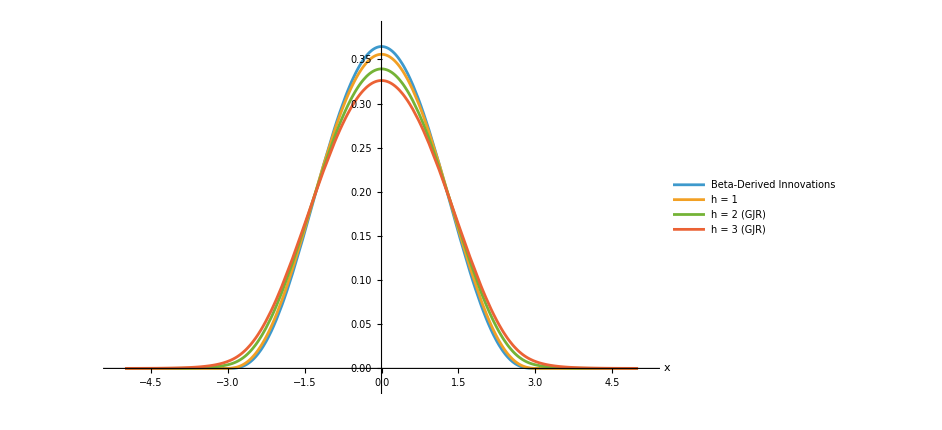

```mathematica
(* ===Right-tail zoom for h=0,1,2,3 ===*)

Plot[Evaluate@{gEps[x],fx1[x],fx2[x], fx3[x]},{x,2,4},PlotRange->All,PlotStyle->{},PlotLegends->Placed[{"Beta-derived innovations","h = 1","h = 2 (GJR)", "h = 3 (GJR)"},{Right,Top}],AxesLabel->{},GridLines->Automatic]
```

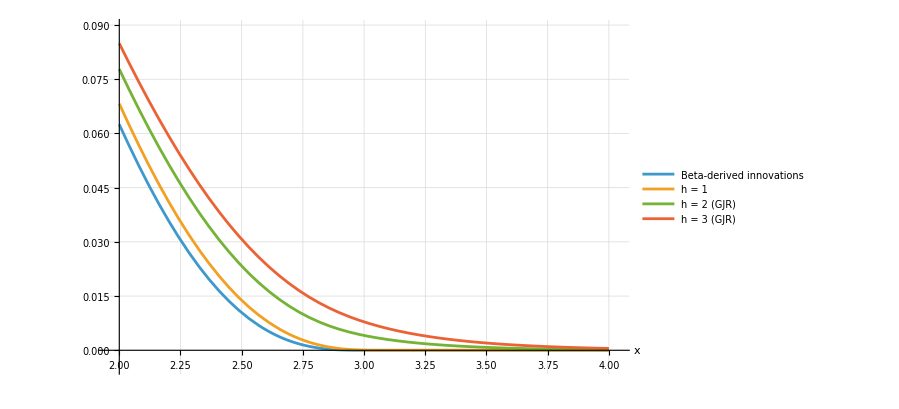

## Two-Step-Ahead Plots with Different Parameters

### Different alpha, beta

```mathematica
(*assumes original definitions of fx2,etc.*)
plot1=Block[{ω=0.1,α=0.1,β=0.85,λ=0.1,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,-5,5},PlotRange->All,PlotStyle->Red,PlotLegends->Placed[{"(0.1, 0.85)"},{Right,Top}]]];

plot2=Block[{ω=0.1,α=0.4,β=0.55,λ=0.1,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,-5,5},PlotRange->All,PlotStyle->Green,PlotLegends->Placed[{"(0.4, 0.55)"},{Right,Top}]]];

plot3=Block[{ω=0.1,α=0.7,β=0.25,λ=0.1,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,-5,5},PlotRange->All,PlotStyle->Blue,PlotLegends->Placed[{"(0.7, 0.25)"},{Right,Top}]]];

plot4=Block[{ω=0.1,α=0.85,β=0.1,λ=0.1,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,-5,5},PlotRange->All,PlotStyle->Orange,PlotLegends->Placed[{"(0.85, 0.1)"},{Right,Top}]]];

Show[plot1,plot2,plot3, plot4]
```

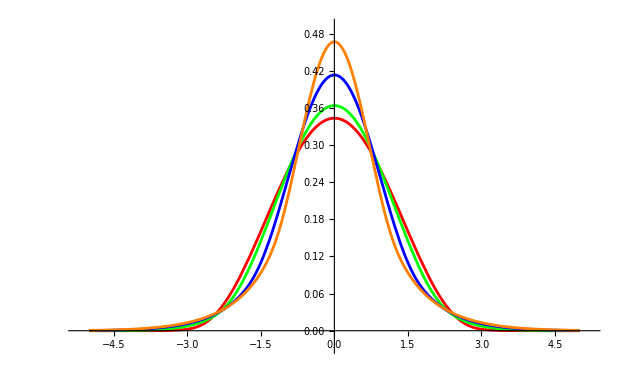

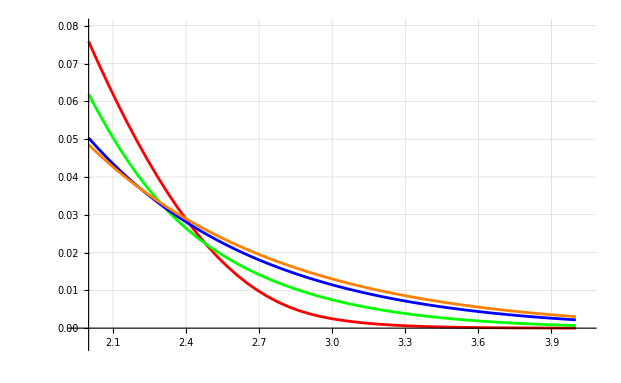

```mathematica
(*assumes original definitions of fx2,etc.*)
plot1=Block[{ω=0.1,α=0.1,β=0.85,λ=0.1,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,2,4},PlotRange->All,PlotStyle->Red,PlotLegends->Placed[{"(0.1, 0.85)"},{Right,Top}], GridLines->Automatic]];

plot2=Block[{ω=0.1,α=0.4,β=0.55,λ=0.1,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,2,4},PlotRange->All,PlotStyle->Green,PlotLegends->Placed[{"(0.4, 0.55)"},{Right,Top}]]];

plot3=Block[{ω=0.1,α=0.7,β=0.25,λ=0.1,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,2,4},PlotRange->All,PlotStyle->Blue,PlotLegends->Placed[{"(0.7, 0.25)"},{Right,Top}]]];

plot4=Block[{ω=0.1,α=0.85,β=0.1,λ=0.1,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,2,4},PlotRange->All,PlotStyle->Orange,PlotLegends->Placed[{"(0.85, 0.1)"},{Right,Top}]]];

Show[plot1,plot2,plot3, plot4]
```

### Different Lambda

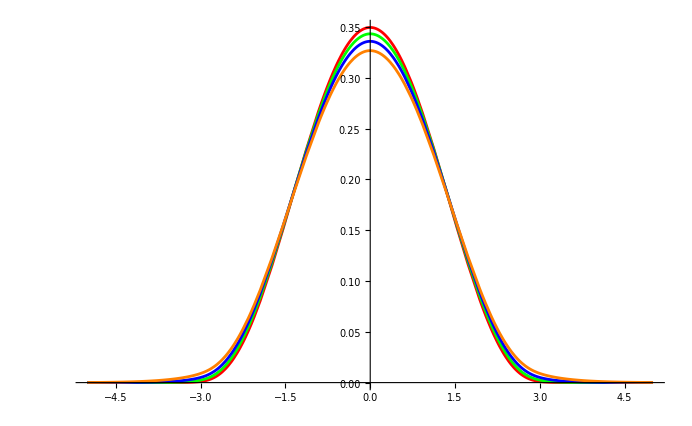

```mathematica
(*assumes original definitions of fx2,etc.*)
plot1=Block[{ω=0.25,α=0.1,β=0.7,λ=0.,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,-5,5},PlotRange->All,PlotStyle->Red,PlotLegends->Placed[{"0 (no assymetry)"},{Right,Top}]]];

plot2=Block[{ω=0.25,α=0.1,β=0.7,λ=0.1,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,-5,5},PlotRange->All,PlotStyle->Green,PlotLegends->Placed[{"0.1"},{Right,Top}]]];

plot3=Block[{ω=0.25,α=0.1,β=0.7,λ=0.25,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,-5,5},PlotRange->All,PlotStyle->Blue,PlotLegends->Placed[{"0.25"},{Right,Top}]]];

plot4=Block[{ω=0.25,α=0.1,β=0.7,λ=0.5,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,-5,5},PlotRange->All,PlotStyle->Orange,PlotLegends->Placed[{"0.5"},{Right,Top}]]];

Show[plot1,plot2,plot3, plot4]
```

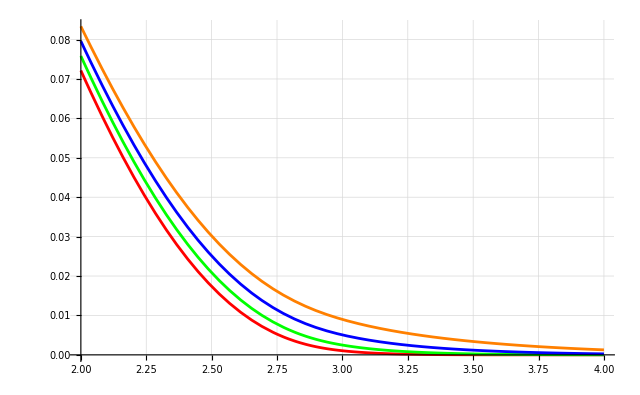

```mathematica
(*assumes original definitions of fx2,etc.*)
plot1=Block[{ω=0.25,α=0.1,β=0.7,λ=0.,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,2,4},PlotRange->All,PlotStyle->Red,PlotLegends->Placed[{"0 (no assymetry)"},{Right,Top}]]];

plot2=Block[{ω=0.25,α=0.1,β=0.7,λ=0.1,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,2,4},PlotRange->All,PlotStyle->Green,PlotLegends->Placed[{"0.1"},{Right,Top}]]];

plot3=Block[{ω=0.25,α=0.1,β=0.7,λ=0.25,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,2,4},PlotRange->All,PlotStyle->Blue,PlotLegends->Placed[{"0.25"},{Right,Top}]]];

plot4=Block[{ω=0.25,α=0.1,β=0.7,λ=0.5,aPar=4,σ1sq=1.05,bPar,Ca,barKappa1,U1,U1max,uMax},bPar=2 aPar+1;
Ca=1/(2^(2 aPar-1) Sqrt[bPar] Beta[aPar,aPar]);
barKappa1=ω+β σ1sq;
U1=bPar*barKappa1;
U1max[s_]:=bPar*(barKappa1+(α+λ(1-s)/2) bPar σ1sq);
uMax=Sqrt[U1max[-1]];
Plot[Evaluate@fx2[u],{u,2,4},PlotRange->All,PlotStyle->Orange,PlotLegends->Placed[{"0.5"},{Right,Top}]]];

Show[plot1,plot2,plot3, plot4]
```